```mathematica
$PlotTheme="Scientific"
```

Scientific

```mathematica
SetOptions[{Plot,ListPlot,ArrayPlot,ContourPlot,DiscretePlot3D},BaseStyle->{14,Directive[FontFamily->"cmr10"]}];
```

# Immirzi 0.1

## Load the Data

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/Spinfoam_radiative_corrections/Notebooks

```mathematica
DATA = "../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/divergence/cutoff_10.0/heptapod_Dl_min_0_Dl_max_10.csv";
```

```mathematica
{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}=Transpose@Import[DATA,"Data",HeaderLines->1];
```

```mathematica
{AKDl0,AKDl1,AKDl2,AKDl3,AKDl4,AKDl5,AKDl6,AKDl7,AKDl8,AKDl9,AKDl10} = Table[{k,#[[2k+1]]},{k,0,10,1/2}]&/@{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10};
```

## Extrapolation using Series convergence acceleration

```mathematica
Aitken[AD_]:=(AD[[-1]]AD[[-3]]-AD[[-2]]^2)/(AD[[-1]]-2AD[[-2]]+AD[[-3]])
```

```mathematica
rExtrapolation= Aitken/@Transpose[{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,1.58448×10^-8,5.71328×10^-8,5.74849×10^-8,6.78594×10^-8,7.43578×10^-8,7.8811×10^-8,8.20546×10^-8,8.45233×10^-8,8.64656×10^-8,8.80339×10^-8,8.93269×10^-8,9.04113×10^-8,9.13339×10^-8,9.21284×10^-8,9.28199×10^-8,9.34271×10^-8,9.39646×10^-8,9.44437×10^-8,9.48735×10^-8,9.52612×10^-8}

```mathematica
Extrapolation=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation]
```

{{0,0},{1/2,1.58448×10^-8},{1,5.71328×10^-8},{3/2,5.74849×10^-8},{2,6.78594×10^-8},{5/2,7.43578×10^-8},{3,7.8811×10^-8},{7/2,8.20546×10^-8},{4,8.45233×10^-8},{9/2,8.64656×10^-8},{5,8.80339×10^-8},{11/2,8.93269×10^-8},{6,9.04113×10^-8},{13/2,9.13339×10^-8},{7,9.21284×10^-8},{15/2,9.28199×10^-8},{8,9.34271×10^-8},{17/2,9.39646×10^-8},{9,9.44437×10^-8},{19/2,9.48735×10^-8},{10,9.52612×10^-8}}

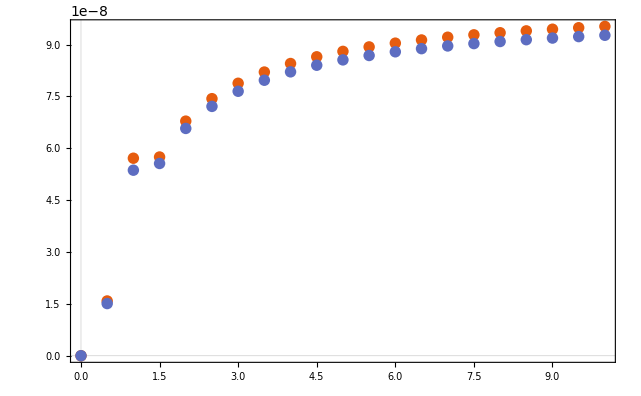

```mathematica
ListPlot[{ Extrapolation,AKDl10}]
```

```mathematica
fitExtrap=NonlinearModelFit[Extrapolation[[5;;]], a Log[k] +b + c/k +d/k^2 ,{a,b,c,d},k]
```

FittedModel[1.02121×10^-7+(1.06981×10^-8)/k^2-(7.41402×10^-8)/k+1.95039×10^-10 Log[k]]

```mathematica
fitExtrap["BestFitParameters"]
```

{a→1.95039×10^-10,b→1.02121×10^-7,c→-7.41402×10^-8,d→1.06981×10^-8}

```mathematica
(Normal[fitExtrap]/.Plus->List)/.k-> 10
```

{1.02121×10^-7,1.06981×10^-10,-7.41402×10^-9,4.49093×10^-10}

```mathematica
Options[GraphicsBox,DefaultBaseStyle]
```

{DefaultBaseStyle→Graphics}

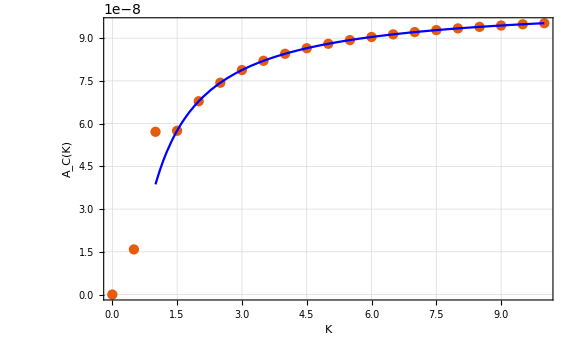

```mathematica
Show[ListPlot[Extrapolation,PlotRange->All,GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large],Plot[Normal@fitExtrap,{k,1,10},PlotStyle->Blue]]
```

```mathematica
fitExtrap=NonlinearModelFit[Extrapolation[[5;;]], b + c/k +d/k^2 ,{b,c,d},k]
```

FittedModel[1.02712×10^-7+(1.22424×10^-8)/k^2-(7.58099×10^-8)/k]

```mathematica
fitExtrap["BestFitParameters"]
```

{b→1.02712×10^-7,c→-7.58099×10^-8,d→1.22424×10^-8}

```mathematica
fitExtrap["ParameterErrors"]
```

{7.81971×10^-12,6.7251×10^-11,1.18389×10^-10}

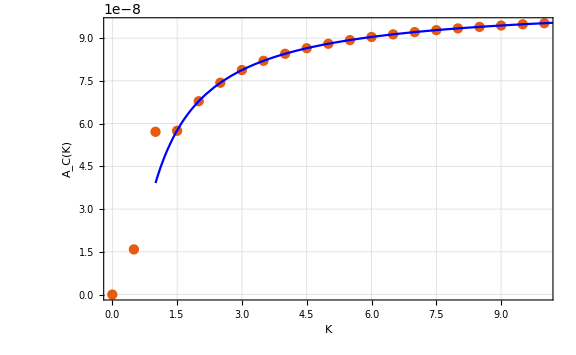

```mathematica
Show[ListPlot[Extrapolation,PlotRange->All,GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large],Plot[Normal@fitExtrap,{k,1,10.5},PlotStyle->Blue]]
```

```mathematica
fitExtrap["BestFitParameters"]
```

{a→1.02259×10^-7,b→-0.729421,c→0.109776,d→0.00148569,e→1.}

{2.76073×10^-11,0.000643357,0.000899981,0.0000865158,0.}

```mathematica
fitExtrap["RSquared"]
```

1.

# Immirzi 0.1 and dimension (2j+1)^2

## Load the Data

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/Spinfoam_radiative_corrections/Notebooks

```mathematica
DATA = "../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/divergence/cutoff_10.0/heptapod_Dl_min_0_Dl_max_10_dim_2.csv";
```

```mathematica
{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}=Transpose@Import[DATA,"Data",HeaderLines->1];
```

```mathematica
{AKDl0,AKDl1,AKDl2,AKDl3,AKDl4,AKDl5,AKDl6,AKDl7,AKDl8,AKDl9,AKDl10} = Table[{k,#[[2k+1]]},{k,0,10,1/2}]&/@{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10};
```

## Extrapolation using Series convergence acceleration

```mathematica
Aitken[AD_]:=(AD[[-1]]AD[[-3]]-AD[[-2]]^2)/(AD[[-1]]-2AD[[-2]]+AD[[-3]])
```

```mathematica
rExtrapolation= Aitken/@Transpose[{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,2.53856×10^-7,9.0241×10^-7,1.4765×10^-6,2.75382×10^-6,4.36398×10^-6,6.29697×10^-6,8.54756×10^-6,0.0000111127,0.0000139904,0.0000171795,0.0000206789,0.0000244881,0.0000286065,0.0000330337,0.0000377694,0.0000428134,0.0000481654,0.0000538253,0.0000597929,0.0000660682}

```mathematica
Extrapolation=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation]
```

{{0,0},{1/2,2.53856×10^-7},{1,9.0241×10^-7},{3/2,1.4765×10^-6},{2,2.75382×10^-6},{5/2,4.36398×10^-6},{3,6.29697×10^-6},{7/2,8.54756×10^-6},{4,0.0000111127},{9/2,0.0000139904},{5,0.0000171795},{11/2,0.0000206789},{6,0.0000244881},{13/2,0.0000286065},{7,0.0000330337},{15/2,0.0000377694},{8,0.0000428134},{17/2,0.0000481654},{9,0.0000538253},{19/2,0.0000597929},{10,0.0000660682}}

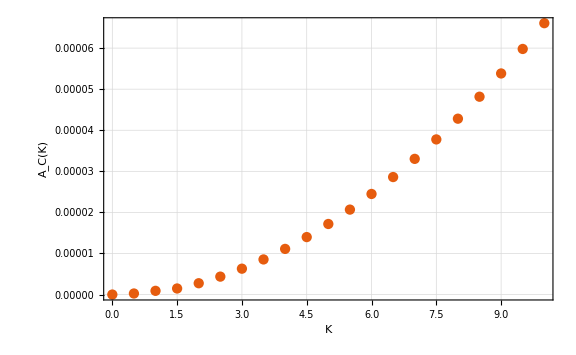

```mathematica
ListPlot[Extrapolation,PlotRange->All,GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large]
```

```mathematica
fitExtrap=NonlinearModelFit[Extrapolation[[5;;]],a k^3+ b k^2 + c k+ d,{a,b,c,d},k]
```

FittedModel[-5.73835×10^-7+3.91509×10^-7 k+6.36217×10^-7 k^2-8.98924×10^-10 k^3]

```mathematica
(Normal[fitExtrap]/.Plus->List)/.k->10
```

{-5.73835×10^-7,3.91509×10^-6,0.0000636217,-8.98924×10^-7}

```mathematica
fitExtrap["BestFitParameters"]
```

{a→-8.98924×10^-10,b→6.36217×10^-7,c→3.91509×10^-7,d→-5.73835×10^-7}

```mathematica
fitExtrap=NonlinearModelFit[Extrapolation[[5;;]],c (1+ a  k + b k^2+ e Log[k]),{a,b,c,e},k]
```

FittedModel[-7.02195×10^-7 (1-0.905194 k-0.873047 k^2+0.551006 Log[k])]

```mathematica
fitExtrap["RSquared"]
```

1.

```mathematica
fitExtrap=NonlinearModelFit[Extrapolation[[5;;]],c (1+ a  k + b k^2),{a,b,c},k]
```

FittedModel[-7.50852×10^-7 (1-0.65493 k-0.824549 k^2)]

```mathematica
fitExtrap["RSquared"]
```

1.

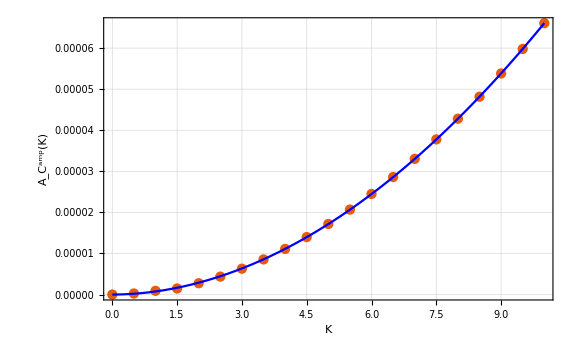

```mathematica
Show[ListPlot[Extrapolation,PlotRange->All,GridLines->Automatic,FrameLabel->{"K","A_C^amp(K)"},ImageSize->Large],Plot[Normal@fitExtrap,{k,0,10},PlotStyle->Blue]]
```

# Immirzi 1

## Load the Data

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/src

```mathematica
DATA = "../2_divergent_diagrams_EPRL/data/EPRL/immirzi_1.0/divergence/cutoff_10.0/heptapod_Dl_min_0_Dl_max_10.csv";
```

```mathematica
{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}=Transpose@Import[DATA,"Data",HeaderLines->1];
```

```mathematica
{AKDl0,AKDl1,AKDl2,AKDl3,AKDl4,AKDl5,AKDl6,AKDl7,AKDl8,AKDl9,AKDl10} = Table[{k,#[[2k+1]]},{k,0,10,1/2}]&/@{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10};
```

## Extrapolation using Series convergence acceleration

```mathematica
Aitken[AD_]:=(AD[[-1]]AD[[-3]]-AD[[-2]]^2)/(AD[[-1]]-2AD[[-2]]+AD[[-3]])
```

```mathematica
rExtrapolation= Aitken/@Transpose[{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,4.71162×10^-14,1.57768×10^-13,2.0262×10^-13,2.65774×10^-13,3.16101×10^-13,3.57125×10^-13,3.91176×10^-13,4.19871×10^-13,4.44368×10^-13,4.65517×10^-13,4.83954×10^-13,5.00167×10^-13,5.14531×10^-13,5.27346×10^-13,5.38846×10^-13,5.49225×10^-13,5.58637×10^-13,5.67211×10^-13,5.75054×10^-13,5.82256×10^-13}

```mathematica
Extrapolation=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1,10,1/2}]&@rExtrapolation]
```

{{0,0},{1,1.57768×10^-13},{3/2,2.0262×10^-13},{2,2.65774×10^-13},{5/2,3.16101×10^-13},{3,3.57125×10^-13},{7/2,3.91176×10^-13},{4,4.19871×10^-13},{9/2,4.44368×10^-13},{5,4.65517×10^-13},{11/2,4.83954×10^-13},{6,5.00167×10^-13},{13/2,5.14531×10^-13},{7,5.27346×10^-13},{15/2,5.38846×10^-13},{8,5.49225×10^-13},{17/2,5.58637×10^-13},{9,5.67211×10^-13},{19/2,5.75054×10^-13},{10,5.82256×10^-13}}

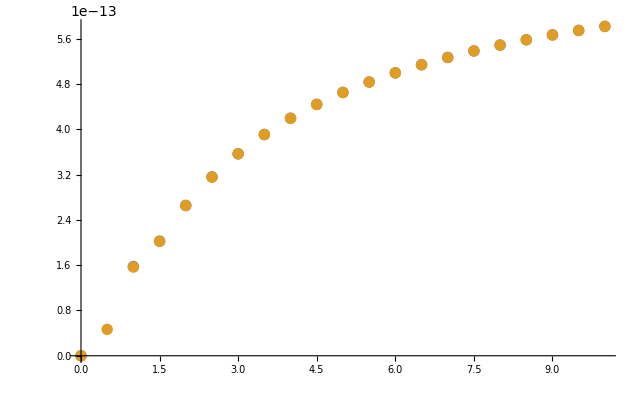

```mathematica
ListPlot[{ Extrapolation,AKDl10}]
```

```mathematica
fitExtrap=NonlinearModelFit[Extrapolation[[5;;]],a(1  + b/k+c/k^2+d Log[k]),{a,b,c,d},k]
```

FittedModel[5.39207×10^-13 (1+1.35172/k^2-1.82204/k+0.108146 Log[k])]

```mathematica
{1,1.3517206628902836/k^2,1.8220416651419578/k,0.1081458772739303 Log[k]}/.k->10
```

{1,0.0135172,0.182204,0.249015}

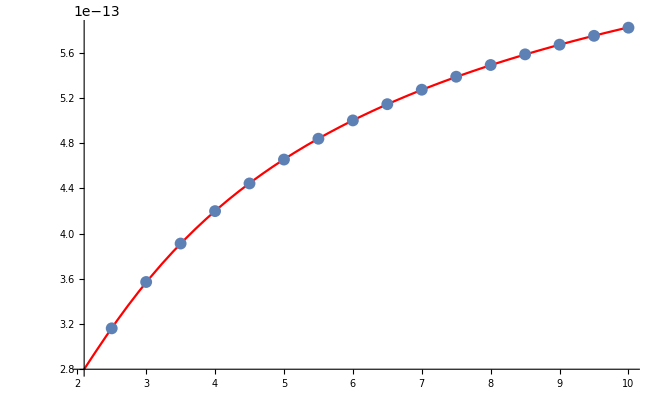

```mathematica
Show[Plot[Normal@fitExtrap,{k,2.1,10},PlotStyle->Red],ListPlot[Extrapolation]]
```

```mathematica
fitExtrap["BestFitParameters"]
```

{a→5.39207×10^-13,b→-1.82204,c→1.35172,d→0.108146}

```mathematica
fitExtrap["ParameterErrors"]
```

{3.68646×10^-16,0.000336825,0.00013288,0.000379339}